```mathematica
ResourceFunction["DarkMode"][]
```

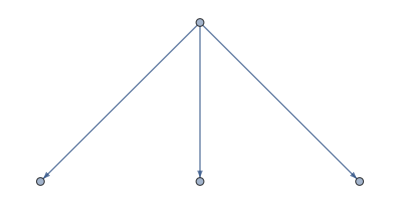

```mathematica
TreeGraph[{1->2,1->3,1->4}]
```

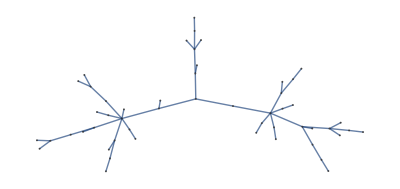

```mathematica
g=TreeGraph[RandomInteger[#]<->#+1&/@Range[0,50],VertexSize->0.1]
```

```mathematica
RandomColor[]
```

RGBColor[0.9768725592437535, 0.8130627321232116, 0.8349011666231958]

```mathematica
RGBColor[1, 0.8, 0]
```

RGBColor[1, 0.8, 0]

```mathematica
colors = RandomColor[RGBColor[1,NormalDistribution[.6,.2],0],10]
```

{RGBColor[1., 0.5851196246341486, 0.],RGBColor[1., 0.5091216863433938, 0.],RGBColor[1., 0.49749192148496546, 0.],RGBColor[1., 0.5864135703367342, 0.],RGBColor[1., 0.4187426682187071, 0.],RGBColor[1., 0.5992233414966225, 0.],RGBColor[1., 0.8567578585522281, 0.],RGBColor[1., 0.6118461803337704, 0.],RGBColor[1., 0.5761355184076534, 0.],RGBColor[1., 0.49962835928890753, 0.]}

```mathematica
colors = {RGBColor[1., 0.5851196246341486, 0.]<->"",RGBColor[1., 0.5091216863433938, 0.]<->"",RGBColor[1., 0.49749192148496546, 0.]<->"",RGBColor[1., 0.5864135703367342, 0.]<->"",RGBColor[1., 0.4187426682187071, 0.]<->"",RGBColor[1., 0.5992233414966225, 0.]<->"",RGBColor[1., 0.8567578585522281, 0.]<->"",RGBColor[1., 0.6118461803337704, 0.]<->"",RGBColor[1., 0.5761355184076534, 0.]<->"",RGBColor[1., 0.49962835928890753, 0.]<->""}
```

{RGBColor[1., 0.5851196246341486, 0.]<->,RGBColor[1., 0.5091216863433938, 0.]<->,RGBColor[1., 0.49749192148496546, 0.]<->,RGBColor[1., 0.5864135703367342, 0.]<->,RGBColor[1., 0.4187426682187071, 0.]<->,RGBColor[1., 0.5992233414966225, 0.]<->,RGBColor[1., 0.8567578585522281, 0.]<->,RGBColor[1., 0.6118461803337704, 0.]<->,RGBColor[1., 0.5761355184076534, 0.]<->,RGBColor[1., 0.49962835928890753, 0.]<->}

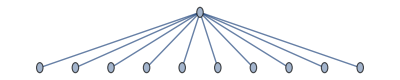

```mathematica
Graph[colors]
```

```mathematica
vertices
```

{0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}

```mathematica
numKids = Map[RandomChoice[{(1-#)*10,5,#*10}->{0,1,2}]&, vertices]
```

{0,1,0,1,1,1,1,2,2,2}

```mathematica
RandomVariate[NormalDistribution[1, 0.1], 1]
```

{1.0955}

```mathematica
childVertices = MapThread[RandomVariate[NormalDistribution[#1, 0.1], #2]&, {vertices, numKids}]
```

{{},{0.19338},{},{0.294069},{0.617736},{0.583476},{0.803249},{0.713472,0.662429},{1.06778,0.91379},{1.04696,0.9503}}

```mathematica
edgeAll[parent_, children_]:= parent-># &/@ children
```

```mathematica
edges  = MapThread[edgeAll, {vertices, childVertices}]
```

{{0.1→0.00938305,0.1→0.173025},{0.2→0.302124,0.2→0.243735},{},{0.4→0.381339},{0.5→0.567443,0.5→0.422376},{0.6→0.515701},{0.7→0.680676,0.7→0.72145},{},{0.9→0.866872,0.9→0.884571},{}}

```mathematica
childCoords = #->{#, 0.9}&/@ Flatten[childVertices]
```

{0.00938305→{0.00938305,0.9},0.173025→{0.173025,0.9},0.302124→{0.302124,0.9},0.243735→{0.243735,0.9},0.381339→{0.381339,0.9},0.567443→{0.567443,0.9},0.422376→{0.422376,0.9},0.515701→{0.515701,0.9},0.680676→{0.680676,0.9},0.72145→{0.72145,0.9},0.866872→{0.866872,0.9},0.884571→{0.884571,0.9}}

```mathematica
childStyles = #->RGBColor[1, #, 0]&/@ Flatten[childVertices]
```

{0.00938305→RGBColor[1, 0.009383046589604968, 0],0.173025→RGBColor[1, 0.17302541580390862, 0],0.302124→RGBColor[1, 0.3021244731454036, 0],0.243735→RGBColor[1, 0.24373529066699323, 0],0.381339→RGBColor[1, 0.3813392182566823, 0],0.567443→RGBColor[1, 0.5674428047139439, 0],0.422376→RGBColor[1, 0.4223758165921097, 0],0.515701→RGBColor[1, 0.5157009361705354, 0],0.680676→RGBColor[1, 0.6806757205466187, 0],0.72145→RGBColor[1, 0.7214504949533946, 0],0.866872→RGBColor[1, 0.8668719876389552, 0],0.884571→RGBColor[1, 0.8845714961759872, 0]}

```mathematica
vertices = Range[0.1, 1, 0.1]
```

{0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}

```mathematica
initialStyles = #->RGBColor[1, #, 0]&/@ vertices
```

{0.1→RGBColor[1, 0.1, 0],0.2→RGBColor[1, 0.2, 0],0.3→RGBColor[1, 0.30000000000000004, 0],0.4→RGBColor[1, 0.4, 0],0.5→RGBColor[1, 0.5, 0],0.6→RGBColor[1, 0.6, 0],0.7→RGBColor[1, 0.7000000000000001, 0],0.8→RGBColor[1, 0.8, 0],0.9→RGBColor[1, 0.9, 0],1.→RGBColor[1, 1., 0]}

```mathematica
coords = #->{#, 1}&/@ vertices
```

{0.1→{0.1,1},0.2→{0.2,1},0.3→{0.3,1},0.4→{0.4,1},0.5→{0.5,1},0.6→{0.6,1},0.7→{0.7,1},0.8→{0.8,1},0.9→{0.9,1},1.→{1.,1}}

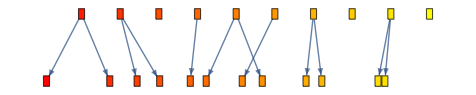

```mathematica
Graph[Join[vertices, Flatten[childVertices]],Flatten[edges], VertexCoordinates->Join[coords, childCoords], VertexStyle->Join[initialStyles, childStyles], VertexShapeFunction->"Square", VertexSize->1]
```

```mathematica
initialVertices = Range[0.1, 1, 0.1];
```

```mathematica
testChildren = getChildren[initialVertices]
```

{{0.0159744,0.242677},{0.155172},{},{0.422409},{0.439256,0.638625},{0.650289,0.587799},{0.77343},{0.790152},{0.776599},{1.05386}}

```mathematica
testEdges = getEdges[initialVertices, testChildren]
```

{0.1→0.0159744,0.1→0.242677,0.2→0.155172,0.4→0.422409,0.5→0.439256,0.5→0.638625,0.6→0.650289,0.6→0.587799,0.7→0.77343,0.8→0.790152,0.9→0.776599,1.→1.05386}

```mathematica
initialVertices
```

{0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}

```mathematica
testInitialCoords = getCoords[initialVertices, 0]
```

{0.1→{0.1,1},0.2→{0.2,1},0.3→{0.3,1},0.4→{0.4,1},0.5→{0.5,1},0.6→{0.6,1},0.7→{0.7,1},0.8→{0.8,1},0.9→{0.9,1},1.→{1.,1}}

```mathematica
testChildCoords = getCoords[Flatten[testChildren], 1]
```

{0.0159744→{0.0159744,9/10},0.242677→{0.242677,9/10},0.155172→{0.155172,9/10},0.422409→{0.422409,9/10},0.439256→{0.439256,9/10},0.638625→{0.638625,9/10},0.650289→{0.650289,9/10},0.587799→{0.587799,9/10},0.77343→{0.77343,9/10},0.790152→{0.790152,9/10},0.776599→{0.776599,9/10},1.05386→{1.05386,9/10}}

```mathematica
testStyles = Join[getStyles[initialVertices], getStyles[Flatten[testChildren]]];
```

```mathematica
getChildren[parents_]:= Module[{numKids, parentsPos},
parentsPos = Map[If[# <0, 0, If[#>1, 1, #]]&, parents];
numKids = Map[RandomChoice[{2/3 - #   / 5, 1/3+# / 5}->{0,2}]&, parentsPos];
MapThread[RandomVariate[NormalDistribution[#1, 0.1], #2]&, {parentsPos, numKids}]
]
```

```mathematica
getEdges[parents_, children_]:= Flatten[MapThread[edgeAll, {parents, children}]]
```

```mathematica
getCoords[vertices_, level_]:=  #->{#, 1-level/10}&/@ vertices
```

```mathematica
getStyles[vertices_]:= #->RGBColor[1, #, 0]&/@ vertices
```

```mathematica
testInitialCoords
```

{0.19338→{0.19338,1},0.294069→{0.294069,1},0.617736→{0.617736,1},0.583476→{0.583476,1},0.803249→{0.803249,1},0.713472→{0.713472,1},0.662429→{0.662429,1},1.06778→{1.06778,1},0.91379→{0.91379,1},1.04696→{1.04696,1},0.9503→{0.9503,1}}

```mathematica
testChildCoords
```

{0.0608824→{0.0608824,9/10},0.363374→{0.363374,9/10},0.33642→{0.33642,9/10},0.395778→{0.395778,9/10},0.352844→{0.352844,9/10},0.580131→{0.580131,9/10},0.920807→{0.920807,9/10},0.77458→{0.77458,9/10},0.931917→{0.931917,9/10},1.21831→{1.21831,9/10}}

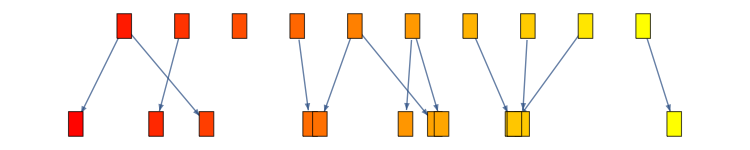

```mathematica
testGraph = Graph[Join[initialVertices, Flatten[testChildren]],testEdges, VertexCoordinates->Join[testInitialCoords, testChildCoords],VertexStyle->testStyles, VertexShapeFunction->"Square"]
```

```mathematica
Flatten[testChildren]
```

{0.0159744,0.242677,0.155172,0.422409,0.439256,0.638625,0.650289,0.587799,0.77343,0.790152,0.776599,1.05386}

```mathematica
tc2 = getChildren[Flatten[testChildren]]
```

{0.0159744,0.242677,0.155172,0.422409,0.439256,0.638625,0.650289,0.587799,0.77343,0.790152,0.776599,1}

{{},{-0.00578894,0.343217},{0.06732},{},{0.385857},{0.624049},{0.585162,0.77883},{0.634392},{0.669002,0.75701},{0.907077},{},{0.962421,1.07374}}

```mathematica
Length[Flatten[testChildren]]
```

12

```mathematica
Length[tc2]
```

12

```mathematica
e2 = getEdges[Flatten[testChildren], tc2]
```

{0.242677→-0.00578894,0.242677→0.343217,0.155172→0.06732,0.439256→0.385857,0.638625→0.624049,0.650289→0.585162,0.650289→0.77883,0.587799→0.634392,0.77343→0.669002,0.77343→0.75701,0.790152→0.907077,1.05386→0.962421,1.05386→1.07374}

```mathematica
c2 = getCoords[Flatten[tc2], 2]
```

{-0.00578894→{-0.00578894,4/5},0.343217→{0.343217,4/5},0.06732→{0.06732,4/5},0.385857→{0.385857,4/5},0.624049→{0.624049,4/5},0.585162→{0.585162,4/5},0.77883→{0.77883,4/5},0.634392→{0.634392,4/5},0.669002→{0.669002,4/5},0.75701→{0.75701,4/5},0.907077→{0.907077,4/5},0.962421→{0.962421,4/5},1.07374→{1.07374,4/5}}

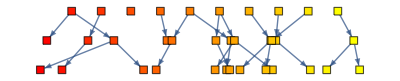

```mathematica
tg2 = Graph[Join[initialVertices, Flatten[testChildren], Flatten[tc2]],Join[testEdges, e2], 
VertexCoordinates->Join[testInitialCoords, testChildCoords, c2],
VertexStyle->ts2, VertexShapeFunction->"Square"]
```

```mathematica
getStyles[Flatten[tc2]]
```

{-0.00578894→RGBColor[1, -0.0057889403209029355, 0],0.343217→RGBColor[1, 0.34321717893780795, 0],0.06732→RGBColor[1, 0.06732004535083752, 0],0.385857→RGBColor[1, 0.3858565594166148, 0],0.624049→RGBColor[1, 0.6240490956446372, 0],0.585162→RGBColor[1, 0.5851615955582786, 0],0.77883→RGBColor[1, 0.7788300629824176, 0],0.634392→RGBColor[1, 0.6343919920383929, 0],0.669002→RGBColor[1, 0.6690018940917184, 0],0.75701→RGBColor[1, 0.7570096702090472, 0],0.907077→RGBColor[1, 0.9070771504041526, 0],0.962421→RGBColor[1, 0.9624205600090809, 0],1.07374→RGBColor[1, 1.0737413376365381, 0]}

```mathematica
ts2 = Join[testStyles, getStyles[Flatten[tc2]]]
```

{0.1→RGBColor[1, 0.1, 0],0.2→RGBColor[1, 0.2, 0],0.3→RGBColor[1, 0.30000000000000004, 0],0.4→RGBColor[1, 0.4, 0],0.5→RGBColor[1, 0.5, 0],0.6→RGBColor[1, 0.6, 0],0.7→RGBColor[1, 0.7000000000000001, 0],0.8→RGBColor[1, 0.8, 0],0.9→RGBColor[1, 0.9, 0],1.→RGBColor[1, 1., 0],0.0159744→RGBColor[1, 0.015974386809854316, 0],0.242677→RGBColor[1, 0.2426770831064927, 0],0.155172→RGBColor[1, 0.15517208050875306, 0],0.422409→RGBColor[1, 0.4224094524512461, 0],0.439256→RGBColor[1, 0.439255966033075, 0],0.638625→RGBColor[1, 0.6386254650785383, 0],0.650289→RGBColor[1, 0.6502886243104703, 0],0.587799→RGBColor[1, 0.5877991774448803, 0],0.77343→RGBColor[1, 0.7734303024511725, 0],0.790152→RGBColor[1, 0.7901522836177682, 0],0.776599→RGBColor[1, 0.7765991967578091, 0],1.05386→RGBColor[1, 1.053862441726067, 0],-0.00578894→RGBColor[1, -0.0057889403209029355, 0],0.343217→RGBColor[1, 0.34321717893780795, 0],0.06732→RGBColor[1, 0.06732004535083752, 0],0.385857→RGBColor[1, 0.3858565594166148, 0],0.624049→RGBColor[1, 0.6240490956446372, 0],0.585162→RGBColor[1, 0.5851615955582786, 0],0.77883→RGBColor[1, 0.7788300629824176, 0],0.634392→RGBColor[1, 0.6343919920383929, 0],0.669002→RGBColor[1, 0.6690018940917184, 0],0.75701→RGBColor[1, 0.7570096702090472, 0],0.907077→RGBColor[1, 0.9070771504041526, 0],0.962421→RGBColor[1, 0.9624205600090809, 0],1.07374→RGBColor[1, 1.0737413376365381, 0]}

```mathematica
getEvolutionGraph[nLevels_]:= Module[{initialVertices, allVerts, allEdges, i, vflat, allCoords, allStyles},
initialVertices = Range[0.1, 1, 0.1];
allVerts = getAllChildren[initialVertices, nLevels - 1];
allEdges = Developer`PartitionMap[getEdges[Flatten[#[[1]]], #[[2]]]&, allVerts, 2, 1];
For[i = 1; vflat = Flatten/@ allVerts; allCoords = {}, 
i <= nLevels, i++, AppendTo[allCoords, getCoords[vflat[[i]], i]]];
allStyles = getStyles[Flatten[allVerts]];
tg2 = Graph[Flatten[allVerts], Flatten[allEdges], VertexCoordinates->Flatten[allCoords], VertexStyle->allStyles, 
VertexShapeFunction->"Square"]
]
```

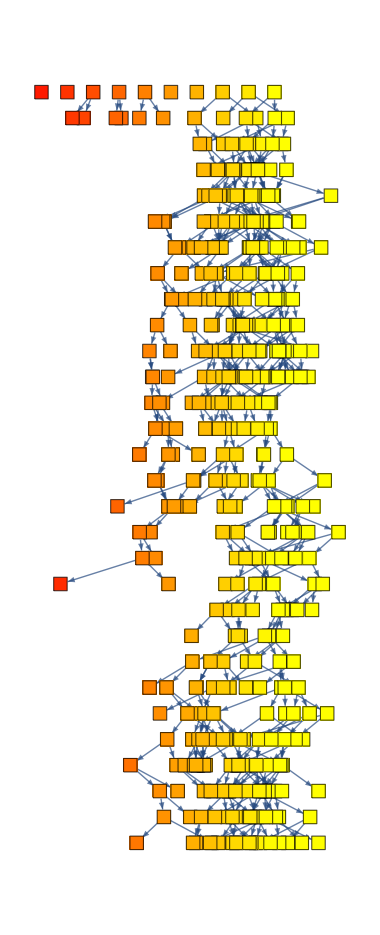

```mathematica
tg3 = getEvolutionGraph[30]
```

```mathematica
initialVertices = Range[0.1, 1, 0.1];
```

```mathematica
allVerts = getAllChildren[initialVertices, 5]
```

{{0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.},{{},{},{0.25966},{},{0.311547},{0.655716,0.878798},{0.812518,0.695065},{0.781104,0.81321},{0.926162},{0.870564,0.931039}},{{},{},{},{0.7989},{0.881659,1.00026},{0.623933,0.716658},{},{},{0.979643,1.10032},{0.750203,0.814385},{1.14327,0.899881}},{{0.929168,0.902208},{0.947699,0.874754},{0.898087},{0.679608},{0.615573,0.654829},{1.03604,0.994895},{1.00867},{0.784372,0.683551},{0.791285},{1.12295,1.00297},{0.810267}},{{1.09763,0.925832},{0.79813},{1.04145,0.960348},{0.917925,0.921044},{1.07885,0.859816},{0.703046},{0.628723},{0.757988},{1.01135,0.971645},{1.00962,1.12629},{1.15974,1.00413},{0.874866,0.967568},{0.666379},{0.64362},{1.05231,1.02775},{1.01387},{0.663769,0.660249}},{{1.0141,1.00336},{0.907071,0.840245},{0.910157},{1.05739,1.00703},{1.05913,0.920013},{0.74017,0.912001},{0.959121},{1.13868,1.04022},{0.975518,1.08443},{},{},{},{0.890589},{0.937512,1.12611},{1.08675,0.951576},{1.03359},{0.990116},{1.0749,1.09849},{0.766618,0.803582},{0.945029,0.972686},{},{0.555042,0.689082},{0.93735,1.01122},{0.971035},{1.0985,0.814001},{},{}}}

```mathematica
allEdges = Developer`PartitionMap[getEdges[Flatten[#[[1]]], #[[2]]]&, allVerts, 2, 1]
```

{{0.3→0.25966,0.5→0.311547,0.6→0.655716,0.6→0.878798,0.7→0.812518,0.7→0.695065,0.8→0.781104,0.8→0.81321,0.9→0.926162,1.→0.870564,1.→0.931039},{0.878798→0.7989,0.812518→0.881659,0.812518→1.00026,0.695065→0.623933,0.695065→0.716658,0.926162→0.979643,0.926162→1.10032,0.870564→0.750203,0.870564→0.814385,0.931039→1.14327,0.931039→0.899881},{0.7989→0.929168,0.7989→0.902208,0.881659→0.947699,0.881659→0.874754,1.00026→0.898087,0.623933→0.679608,0.716658→0.615573,0.716658→0.654829,0.979643→1.03604,0.979643→0.994895,1.10032→1.00867,0.750203→0.784372,0.750203→0.683551,0.814385→0.791285,1.14327→1.12295,1.14327→1.00297,0.899881→0.810267},{0.929168→1.09763,0.929168→0.925832,0.902208→0.79813,0.947699→1.04145,0.947699→0.960348,0.874754→0.917925,0.874754→0.921044,0.898087→1.07885,0.898087→0.859816,0.679608→0.703046,0.615573→0.628723,0.654829→0.757988,1.03604→1.01135,1.03604→0.971645,0.994895→1.00962,0.994895→1.12629,1.00867→1.15974,1.00867→1.00413,0.784372→0.874866,0.784372→0.967568,0.683551→0.666379,0.791285→0.64362,1.12295→1.05231,1.12295→1.02775,1.00297→1.01387,0.810267→0.663769,0.810267→0.660249},{1.09763→1.0141,1.09763→1.00336,0.925832→0.907071,0.925832→0.840245,0.79813→0.910157,1.04145→1.05739,1.04145→1.00703,0.960348→1.05913,0.960348→0.920013,0.917925→0.74017,0.917925→0.912001,0.921044→0.959121,1.07885→1.13868,1.07885→1.04022,0.859816→0.975518,0.859816→1.08443,1.01135→0.890589,0.971645→0.937512,0.971645→1.12611,1.00962→1.08675,1.00962→0.951576,1.12629→1.03359,1.15974→0.990116,1.00413→1.0749,1.00413→1.09849,0.874866→0.766618,0.874866→0.803582,0.967568→0.945029,0.967568→0.972686,0.64362→0.555042,0.64362→0.689082,1.05231→0.93735,1.05231→1.01122,1.02775→0.971035,1.01387→1.0985,1.01387→0.814001}}

```mathematica
Length/@ allEdges
```

{11,11,17,27,36}

```mathematica
For[i = 1; vflat = Flatten/@ allVerts; allCoords = {}, 
i <= 5, i++, AppendTo[allCoords, getCoords[vflat[[i]], i]]]
```

```mathematica
Length/@allCoords
```

{10,11,11,17,27}

```mathematica
Length/@allCoords
```

{10,11,11,17,27}

```mathematica
allStyles = getStyles[Flatten[allVerts]];
Print[Length[allVerts]];
tg2 = Graph[Flatten[allVerts], Flatten[allEdges], VertexCoordinates->FlallCoords, VertexStyle->allStyles, 
VertexShapeFunction->"Square"]
```

```mathematica
getAllChildren[initialVertices, 3]
```

{{0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.},{{},{},{},{0.337021,0.479254},{},{},{},{0.987416},{0.897236},{0.949886}},{{0.444402},{0.522022},{0.919714,1.0016},{0.927589,0.879928},{0.94864}},{{},{0.445129},{0.987999,0.887748},{0.988486,1.10924},{1.02817,1.03271},{0.98206,0.751006},{1.08917}}}

```mathematica
getEvolutionGraph[2]
```

3

```mathematica
getAllChildren[initial_, nLevels_]:=
NestList[getChildren[Flatten[#]]&, initial, nLevels]
```

```mathematica
Length[ac[[3]]]
```

11

```mathematica
NestList[#+1&, 0, 10]
```

{0,1,2,3,4,5,6,7,8,9,10}